```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/akapiisp/Documents/research/Self-similar approximations

Maybe I should use the Borel self similar summation technique discussed in 2505.12119 to get real solutions

### With pressure Nsolve:

```mathematica
Iorder = 1;
Ttable = Table[i,{i,80,300,2}];
μtable = Table[i/j,{j,80,300,2},{i,0,800,800/Length[Ttable]}];
Pfunc[T_] =  Interpolation[Pdata,InterpolationOrder->Iorder][T];
chi2func[T_] = Interpolation[chi2,InterpolationOrder->Iorder][T];
chi4func[T_] = Interpolation[chi4,InterpolationOrder->Iorder][T];
chi6func[T_] = Interpolation[chi6,InterpolationOrder->Iorder][T];
chi8func[T_] = Interpolation[chi8,InterpolationOrder->Iorder][T];
chi10func[T_] = Interpolation[chi10,InterpolationOrder->Iorder][T];

Plist = Pfunc[Ttable];
chi2list = chi2func[Ttable];
chi4list = chi4func[Ttable];
chi6list = chi6func[Ttable];
chi8list = chi8func[Ttable];
chi10list = chi10func[Ttable];
```

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

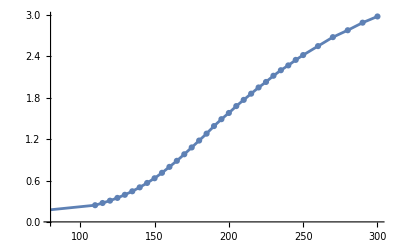

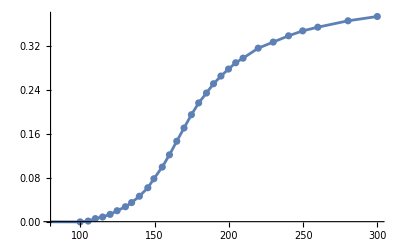

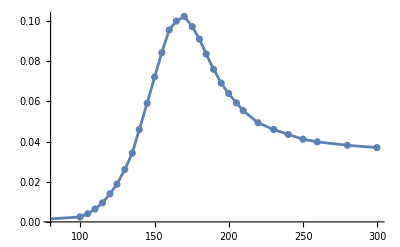

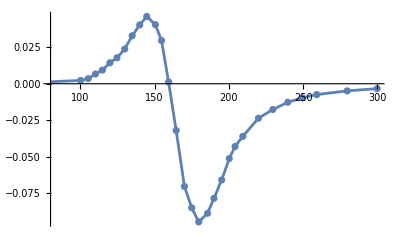

```mathematica
Show[{Plot[Pfunc[T],{T,80,300}],ListPlot[Pdata]}]
Show[{Plot[chi2func[T],{T,80,300}],ListPlot[chi2]}]
Show[{Plot[chi4func[T],{T,80,300}],ListPlot[chi4]}]
Show[{Plot[chi6func[T],{T,80,300}],ListPlot[chi6]}]
```

```mathematica
P={};
For[i=1,i≤Length[Ttable],i++,coeffs={1,chi2list⟦i⟧/(2! Plist⟦i⟧),chi4list⟦i⟧/(4! Plist⟦i⟧),chi6list⟦i⟧/(6! Plist⟦i⟧),chi8list⟦i⟧/(8! Plist⟦i⟧),chi10list⟦i⟧/(10! Plist⟦i⟧)};x=Symbol["x"];k=Length[coeffs]-1;m=(k+1)/2;At=Table[A[j],{j,1,m}];
nt=Table[n[j],{j,1,m}];

(*---Construct factor approximant---*)
factorApprox=Times@@Table[(1+At[[i]] x)^nt[[i]],{i,1,m}];

(*---Expand and collect series---*)
seriesApprox=Normal[Series[factorApprox,{x,0,k}]];

(*---Create equations by matching coefficients---*)
equations=Table[Coefficient[seriesApprox,x,j-1]==coeffs[[j]],{j,1,k+1}];
(*Should probably also have AppendTo[equations,Total[nt]=2]*)

(*---Solve for parameters---*)
(*Solve over reals, maybe the exponents could be complex for DSI*)
solutions=NSolve[equations,Join[At,nt]];

(*---Factor approximant with solved parameters---*)
factorApproximant=Plist[[i]]*factorApprox/. solutions /. x-> μ^2;
aux ={{factorApproximant}};
For[j=1,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,factorApproximant/.μ->μtable⟦i,j⟧}];];

AppendTo[P,aux];
Print[i];Export["withpressureNsolve.mx",P]];
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

1

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

2

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

General::stop: Further output of NSolve::infsolns will be suppressed during this calculation.

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

```mathematica
P = Import["withpressureNsolve.mx"];
results = {#[[1]],#[[2]],Re[#[[3,1]]]} &/@Flatten[P[[;;,2;;]],1];
```

```mathematica
ListPointPlot3D[results[[;;]],AxesLabel->{"μ","T","P"},PlotRange->{{0,800},{80,300},{0,5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

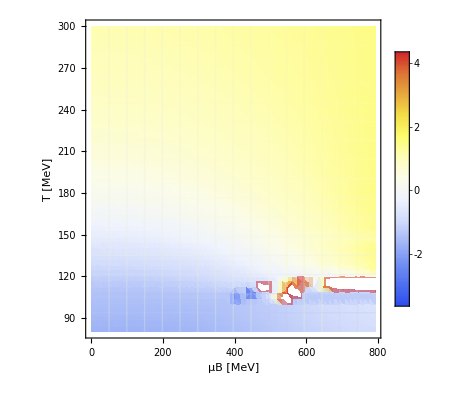

```mathematica
(*Import your data*)

indicesToAverage = Table[i,{i,1,24}];
P=Import["withpressureNsolve.mx"];

(*Flatten your data*)flatData=Flatten[P[[;;;;2,2;;;;2]],1];

(*Compute {x,y,avg z over selected indices}*)
results={#[[1]],#[[2]],Mean[Re/@#[[3,indicesToAverage]]]}&/@flatData;

(*Apply logarithm safely*)
results[[All,3]]=Log[results[[All,3]]];  (*small shift to avoid log(0)*)

(*Plot heatmap*)
ListDensityPlot[results,ColorFunction->"TemperatureMap",InterpolationOrder->1,(*or 2 for smoother*)Frame->True,FrameLabel->{"μB [MeV]","T [MeV]"},PlotLegends->Automatic,Mesh->True]
```

```mathematica
P = Import["withpressuregoal.mx"];
results = {#[[1]],#[[2]],Re[#[[3]]]}&/@P;
```

```mathematica
ListPointPlot3D[results,AxesLabel->{"μ","T","P"},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

### With pressure findroot:

```mathematica
Ttable = Table[i,{i,100,300,5}];
μtable = Table[i/j,{j,100,300,5},{i,0,600,600/Length[Ttable]}];
Pfunc[T_] =  Interpolation[Pdata][T];
chi2func[T_] = Interpolation[chi2][T];
chi4func[T_] = Interpolation[chi4][T];
chi6func[T_] = Interpolation[chi6][T];
chi8func[T_] = Interpolation[chi8][T];
chi10func[T_] = Interpolation[chi10][T];

Plist = Pfunc[Ttable];
chi2list = chi2func[Ttable];
chi4list = chi4func[Ttable];
chi6list = chi6func[Ttable];
chi8list = chi8func[Ttable];
chi10list = chi10func[Ttable];
```

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {105} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100.004} lies outside the range of data in the interpolating function. Extrapolation will be used.

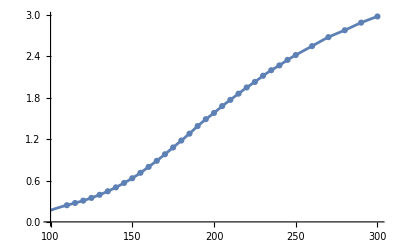

```mathematica
Show[{Plot[Pfunc[T],{T,100,300}],ListPlot[Pdata]}]
```

```mathematica
P={};
For[i=1,i≤Length[Ttable],i++,coeffs={1,chi2list⟦i⟧/(2! Plist⟦i⟧),chi4list⟦i⟧/(4! Plist⟦i⟧),chi6list⟦i⟧/(6! Plist⟦i⟧),chi8list⟦i⟧/(8! Plist⟦i⟧),chi10list⟦i⟧/(10! Plist⟦i⟧)};x=Symbol["x"];k=Length[coeffs]-1;m=(k+1)/2;At=Table[A[j],{j,1,m}];nt=Table[n[j],{j,1,m}];factorApprox=Times@@Table[(1+At⟦i⟧ x)^nt⟦i⟧,{i,1,m}];seriesApprox=Normal[Series[factorApprox,{x,0,k}]];equations=Table[Coefficient[seriesApprox,x,j-1]==coeffs⟦j⟧,{j,1,k+1}];AppendTo[equations,Total[nt]==2];

vars = Join[At,nt];

numSamples=500;  (*increase for more exhaustive search*)

guesses=Table[Thread[{vars,RandomReal[{0,1},Length[vars]]}],{numSamples}];
solutions = {};
For[j=1,j<=Length[guesses],j++,
aux = FindRoot[equations[[2;;]],guesses[[j]],MaxIterations->1000,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->30,Method ->{"Newton","StepControl"->"LineSearch"}];AppendTo[solutions,aux];
];

residual[sol_]:=Norm[equations/. sol];
(*Sort solutions by residual*)
sorted=SortBy[solutions,residual];
(*Best solution*)
bestSolution=First[sorted];
Print[bestSolution];

factorApproximant=Plist⟦i⟧ factorApprox/.bestSolution/.x->μ^2;For[j=1,j≤Length[μtable⟦i⟧],j++,AppendTo[P,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,factorApproximant/.μ->μtable⟦i,j⟧,factorApproximant}];];Print[i];Export["withpressureFindroot.mx",P]];
```

FindRoot::bdmtd: Value of option Method -> Broyden is not Automatic, Brent, Secant, AffineCovariantNewton or Newton.

General::stop: Further output of FindRoot::bdmtd will be suppressed during this calculation.

{A[1]→0.0177424,A[2]→0.326806,A[3]→0.172519,n[1]→0.246512,n[2]→0.705415,n[3]→0.717789}

1

{A[1]→0.00105472,A[2]→0.78352,A[3]→0.531587,n[1]→0.624941,n[2]→0.909638,n[3]→0.215794}

2

{A[1]→0.0099634,A[2]→0.0241986,A[3]→0.441887,n[1]→0.717479,n[2]→0.528277,n[3]→0.144944}

3

{A[1]→0.0130232,A[2]→0.690224,A[3]→0.642239,n[1]→0.683752,n[2]→0.58088,n[3]→0.342469}

4

{A[1]→0.0190676,A[2]→0.193201,A[3]→0.0273185,n[1]→0.8292,n[2]→0.367645,n[3]→0.818123}

5

{A[1]→0.000846837,A[2]→0.0364773,A[3]→0.693786,n[1]→0.286639,n[2]→0.580737,n[3]→0.112303}

6

{A[1]→0.0420513,A[2]→0.66165,A[3]→0.730766,n[1]→0.503454,n[2]→0.653311,n[3]→0.672223}

7

{A[1]→0.00712837,A[2]→0.460375,A[3]→0.0345844,n[1]→0.413048,n[2]→0.460246,n[3]→0.618097}

8

{A[1]→0.0150954,A[2]→0.639884,A[3]→0.910961,n[1]→0.830037,n[2]→0.393675,n[3]→0.944466}

9

{A[1]→0.00749168,A[2]→0.0452797,A[3]→0.815105,n[1]→0.958069,n[2]→0.117372,n[3]→0.704723}

10

{A[1]→0.0390757,A[2]→0.0540821,A[3]→0.028418,n[1]→0.381286,n[2]→0.688466,n[3]→0.114333}

11

{A[1]→0.0259867,A[2]→0.695929,A[3]→0.686967,n[1]→0.909523,n[2]→0.0392408,n[3]→0.0104807}

12

{A[1]→0.0266577,A[2]→0.485257,A[3]→0.228922,n[1]→0.537475,n[2]→0.202496,n[3]→0.659196}

13

{A[1]→0.0573888,A[2]→0.514294,A[3]→0.147228,n[1]→0.307041,n[2]→0.378488,n[3]→0.986821}

14

{A[1]→0.0111377,A[2]→0.913931,A[3]→0.549717,n[1]→0.553079,n[2]→0.863242,n[3]→0.0933617}

15

{A[1]→0.00411093,A[2]→0.135627,A[3]→0.30923,n[1]→0.310791,n[2]→0.261797,n[3]→0.668233}

16

{A[1]→0.00721259,A[2]→0.695533,A[3]→0.762281,n[1]→0.542402,n[2]→0.483982,n[3]→0.397504}

17

{A[1]→0.0161282,A[2]→0.615108,A[3]→0.814701,n[1]→0.511201,n[2]→0.2934,n[3]→0.726657}

18

{A[1]→0.000820768,A[2]→0.563852,A[3]→0.474354,n[1]→0.46718,n[2]→0.324087,n[3]→0.809212}

19

{A[1]→0.0111926,A[2]→0.0895856,A[3]→0.256973,n[1]→0.26659,n[2]→0.599948,n[3]→0.205044}

20

{A[1]→0.000146342,A[2]→0.0876171,A[3]→0.815531,n[1]→0.120285,n[2]→0.994306,n[3]→0.933678}

21

{A[1]→0.0339042,A[2]→0.999114,A[3]→0.144805,n[1]→0.249597,n[2]→0.356469,n[3]→0.797136}

22

{A[1]→0.0335756,A[2]→0.635172,A[3]→0.360719,n[1]→0.428672,n[2]→0.482197,n[3]→0.0784988}

23

{A[1]→0.00494256,A[2]→0.345796,A[3]→0.288918,n[1]→0.575705,n[2]→0.306533,n[3]→0.819693}

24

{A[1]→0.0785236,A[2]→0.379845,A[3]→0.364332,n[1]→0.0641294,n[2]→0.423654,n[3]→0.526561}

25

{A[1]→0.00274894,A[2]→0.332352,A[3]→0.449719,n[1]→0.118623,n[2]→0.671593,n[3]→0.57182}

26

{A[1]→0.017341,A[2]→0.437574,A[3]→0.807655,n[1]→0.218658,n[2]→0.587355,n[3]→0.921625}

27

{A[1]→0.0181557,A[2]→0.565767,A[3]→0.751453,n[1]→0.240333,n[2]→0.0190544,n[3]→0.92876}

28

{A[1]→0.012113,A[2]→0.180013,A[3]→0.667249,n[1]→0.824121,n[2]→0.638786,n[3]→0.708467}

29

{A[1]→0.0110696,A[2]→0.740225,A[3]→0.588835,n[1]→0.193657,n[2]→0.659151,n[3]→0.73426}

30

{A[1]→0.0350737,A[2]→0.352897,A[3]→0.970016,n[1]→0.602889,n[2]→0.562377,n[3]→0.330638}

31

{A[1]→0.00193003,A[2]→0.737546,A[3]→0.281248,n[1]→0.468644,n[2]→0.0863991,n[3]→0.941816}

32

{A[1]→0.0297712,A[2]→0.685537,A[3]→0.991542,n[1]→0.791332,n[2]→0.982881,n[3]→0.14679}

33

{A[1]→0.0114115,A[2]→0.250735,A[3]→0.456026,n[1]→0.876268,n[2]→0.130396,n[3]→0.746724}

34

{A[1]→0.00456489,A[2]→0.000267459,A[3]→0.0672811,n[1]→0.3886,n[2]→0.490416,n[3]→0.439381}

35

{A[1]→0.000669452,A[2]→0.357204,A[3]→0.103695,n[1]→0.678751,n[2]→0.459492,n[3]→0.969431}

36

{A[1]→0.000410686,A[2]→0.97328,A[3]→0.491351,n[1]→0.593412,n[2]→0.344557,n[3]→0.277431}

37

{A[1]→0.00662512,A[2]→0.268604,A[3]→0.266623,n[1]→0.941997,n[2]→0.796401,n[3]→0.359053}

38

{A[1]→0.00641676,A[2]→0.551743,A[3]→0.365106,n[1]→0.210046,n[2]→0.457463,n[3]→0.970229}

39

{A[1]→0.0144424,A[2]→0.670971,A[3]→0.437292,n[1]→0.698498,n[2]→0.0278254,n[3]→0.288876}

40

{A[1]→0.00134025,A[2]→0.406571,A[3]→0.883405,n[1]→0.578249,n[2]→0.414249,n[3]→0.90113}

41

```mathematica
P = Import["withpressureFindroot.mx"];
results = {#[[1]],#[[2]],Re[#[[3]]]}&/@P;
```

```mathematica
ListPointPlot3D[results,AxesLabel->{"μ","T","P"},PlotRange->{{0,600},{100,300},{0,5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

```mathematica
P={};
For[i=1,i≤Length[Ttable],i++,coeffs={1,chi2list⟦i⟧/(2! Plist⟦i⟧),chi4list⟦i⟧/(4! Plist⟦i⟧),chi6list⟦i⟧/(6! Plist⟦i⟧),chi8list⟦i⟧/(8! Plist⟦i⟧),chi10list⟦i⟧/(10! Plist⟦i⟧)};x=Symbol["x"];k=Length[coeffs]-1;m=(k+1)/2;At=Table[A[j],{j,1,m}];nt=Table[n[j],{j,1,m}];factorApprox=Times@@Table[(1+At⟦i⟧ x)^nt⟦i⟧,{i,1,m}];seriesApprox=Normal[Series[factorApprox,{x,0,k}]];equations=Table[Coefficient[seriesApprox,x,j-1]==coeffs⟦j⟧,{j,1,k+1}];AppendTo[equations,Total[nt]==2];

vars = Join[At,nt];

numSamples=1;  (*increase for more exhaustive search*)

guesses=Table[Thread[{vars,-20,100}],{numSamples}];
solutions = {};
For[j=1,j<=Length[guesses],j++,
aux = FindRoot[equations[[2;;]],guesses[[j]],MaxIterations->1000,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->30,Method -> "Secant"];AppendTo[solutions,aux];
];

residual[sol_]:=Norm[equations/. sol];
(*Sort solutions by residual*)
sorted=SortBy[solutions,residual];
(*Best solution*)
bestSolution=First[sorted];
Print[bestSolution];

factorApproximant=Plist⟦i⟧ factorApprox/.bestSolution/.x->μ^2;For[j=1,j≤Length[μtable⟦i⟧],j++,AppendTo[P,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,factorApproximant/.μ->μtable⟦i,j⟧,factorApproximant}];];Print[i];Export["withpressureFindroot.mx",P]];
```

FindRoot::precw: The precision of the argument function ({A[1] n[1]+A[2] n[2]+A[3] n[3]==-0.00134705,1/2 (-A[1]^2 n[1]+A[1]^2 n[1]^2-A[2]^2 n[2]+2 A[1] A[2] n[1] n[2]+A[2]^2 n[2]^2-A[3]^2 n[3]+2 A[1] A[3] n[1] n[3]+2 A[2] A[3] n[2] n[3]+A[3]^2 n[3]^2)==0.000622489,«1»==«24»,«1»,1/120 («1»)+«9»+1/120 («1»)==«23»,n[1]+n[2]+n[3]==2}) is less than WorkingPrecision (30.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{A[1]→164.491910220476313309394685891,A[2]→-151.289759896191680403646821473,A[3]→107.53123360886731708557003527,n[1]→44.3433085433018736562104852511,n[2]→-22.5501396065440265035622736471,n[3]→-19.7931689367578471526482116041}

1

FindRoot::precw: The precision of the argument function ({A[1] n[1]+A[2] n[2]+A[3] n[3]==0.00203825,1/2 (-A[1]^2 n[1]+A[1]^2 n[1]^2-A[2]^2 n[2]+2 A[1] A[2] n[1] n[2]+A[2]^2 n[2]^2-A[3]^2 n[3]+2 A[1] A[3] n[1] n[3]+2 A[2] A[3] n[2] n[3]+A[3]^2 n[3]^2)==0.000814317,«1»==«24»,«1»,1/120 («1»)+«9»+1/120 («1»)==-«23»,n[1]+n[2]+n[3]==2}) is less than WorkingPrecision (30.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{A[1]→164.491754263016070543735799428,A[2]→-151.289880884305741488288833102,A[3]→107.531267067725678400202709114,n[1]→44.3433090503643053031989485039,n[2]→-22.5501401667524162606003548104,n[3]→-19.7931688836118890425985936935}

2

FindRoot::precw: The precision of the argument function ({A[1] n[1]+A[2] n[2]+A[3] n[3]==0.0112654,1/2 (-A[1]^2 n[1]+A[1]^2 n[1]^2-A[2]^2 n[2]+2 A[1] A[2] n[1] n[2]+A[2]^2 n[2]^2-A[3]^2 n[3]+2 A[1] A[3] n[1] n[3]+2 A[2] A[3] n[2] n[3]+A[3]^2 n[3]^2)==0.0011094,«1»==«23»,«1»,1/120 («1»)+«9»+1/120 («1»)==-«21»,n[1]+n[2]+n[3]==2}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{A[1]→164.491329194197211053353703317,A[2]→-151.29021067651167544070876607,A[3]→107.531358269334917249067362544,n[1]→44.3433104324766674162979843544,n[2]→-22.5501416937265297020013830744,n[3]→-19.79316873875013771429660128}

3

{A[1]→164.491135759685802798016127776,A[2]→-151.290360723487616522626570251,A[3]→107.531399764923991684482211472,n[1]→44.3433110613485500632109094722,n[2]→-22.5501423885111352637278122757,n[3]→-19.7931686728374147994830971965}

4

{A[1]→164.490865947425913092945982127,A[2]→-151.290570020951273261627459201,A[3]→107.531457646108953995512312059,n[1]→44.3433119385430323803812586138,n[2]→-22.5501433576453519440099155302,n[3]→-19.7931685808976804363713430836}

5

{A[1]→164.490514114526957259780709383,A[2]→-151.29084296861000176829054542,A[3]→107.531533128750537198602525672,n[1]→44.3433130824665246754752164943,n[2]→-22.5501446214651373734349787849,n[3]→-19.7931684610013873020402377094}

6

{A[1]→164.490290613246068334363552535,A[2]→-151.291016326118839657369715259,A[3]→107.531581071381819474031269288,n[1]→44.3433138090566347115350231386,n[2]→-22.5501454242096890818505679669,n[3]→-19.7931683848469456296844551717}

7

{A[1]→164.490003073794956524691621826,A[2]→-151.291239379513509459717461868,A[3]→107.531642756605908219125233314,n[1]→44.3433147438989408099959527432,n[2]→-22.5501464570338935968961867688,n[3]→-19.7931682868650472130997659744}

8

{A[1]→164.489699147544645729321033991,A[2]→-151.291475113846207997159854363,A[3]→107.531707949955073330400125246,n[1]→44.3433157319357364945544178462,n[2]→-22.5501475486274488951689650197,n[3]→-19.7931681833082875993854528265}

9

{A[1]→164.489397692546766693193047372,A[2]→-151.291708962740928138577900204,A[3]→107.531772620651737443800986057,n[1]→44.343316712023445224876820751,n[2]→-22.550148631439258555551427241,n[3]→-19.7931680805841866693253935101}

10

{A[1]→164.48894698217049892744760565,A[2]→-151.292058636132519589811429039,A[3]→107.531869320866546844478771191,n[1]→44.3433181774828479141589745877,n[2]→-22.5501502504957667967981170706,n[3]→-19.7931679269870811173608575171}

11

{A[1]→164.488660730119976259741879613,A[2]→-151.292280725927307405043736441,A[3]→107.53193073826177215238062392,n[1]→44.3433191082366064284189418128,n[2]→-22.5501512788033956106443596532,n[3]→-19.7931678294332108177745821596}

12

{A[1]→164.488342616493626533158831766,A[2]→-151.292527562036597815233334404,A[3]→107.531998998048602429952081955,n[1]→44.3433201426603444602100621429,n[2]→-22.5501524216472382502775174387,n[3]→-19.7931677210131062099325447042}

13

{A[1]→164.488038422365549039565032331,A[2]→-151.292763646816812533938265897,A[3]→107.532064282740543609276149406,n[1]→44.3433211319544251983602162448,n[2]→-22.5501535146320704119498771331,n[3]→-19.7931676173223547864103391116}

14

{A[1]→164.487828325583531254686553933,A[2]→-151.292926728655528724058458,A[3]→107.532109378861443964710752282,n[1]→44.3433218152969103983407847518,n[2]→-22.5501542695980514778126402978,n[3]→-19.793167545698858920528144454}

15

{A[1]→164.487680625292810857100109817,A[2]→-151.293041423562551200690105632,A[3]→107.53214109297753538596998932,n[1]→44.3433222958192148986024047471,n[2]→-22.5501548004863140110114425524,n[3]→-19.7931674953329008875909621947}

16

{A[1]→164.487610134852084414030905066,A[2]→-151.2930962025202329036428967,A[3]→107.532156238233544587317228324,n[1]→44.3433225252585298866326656346,n[2]→-22.5501550539749688466013231192,n[3]→-19.7931674712835610400313425155}

17

{A[1]→164.487633645902062082872985238,A[2]→-151.293078035626114348834978974,A[3]→107.532151211377180990934515516,n[1]→44.3433224490107775896607415681,n[2]→-22.550154969736766347038035194,n[3]→-19.7931674792740112426227063741}

18

{A[1]→164.487675476219114845790168388,A[2]→-151.293045642764855220525657658,A[3]→107.532142250934012162892843545,n[1]→44.3433223131628750930094921508,n[2]→-22.5501548196514167570767600333,n[3]→-19.7931674935114583359327321175}

19

{A[1]→164.487741350714220497418551899,A[2]→-151.2929945768317643451695459,A[3]→107.532128127300847007210975363,n[1]→44.3433220990856389863860891569,n[2]→-22.550154583137093765386901753,n[3]→-19.7931675159485452209991874039}

20

{A[1]→164.487793651449526323777416489,A[2]→-151.292954030004123172808843729,A[3]→107.532116913133763929608336597,n[1]→44.3433219291112910037137671542,n[2]→-22.5501543953479572937222113681,n[3]→-19.7931675337633337099915557861}

21

{A[1]→164.487875043384167303553949728,A[2]→-151.292890904314743296900356856,A[3]→107.53209945526505778829366203,n[1]→44.3433216645238328776957453528,n[2]→-22.550154103029020779674101341,n[3]→-19.7931675614948120980216440118}

22

{A[1]→164.487970339665843273612645802,A[2]→-151.292816984159577134106415924,A[3]→107.532079012525982124858835642,n[1]→44.3433213547080750751448623849,n[2]→-22.5501537607412224899694185008,n[3]→-19.7931675939668525851754438841}

23

{A[1]→164.488060650178469359284155817,A[2]→-151.292746927907574647067224499,A[3]→107.532059638494166620113200585,n[1]→44.3433210610921369035859271923,n[2]→-22.5501534363511019959432358546,n[3]→-19.7931676247410349076426913377}

24

{A[1]→164.488117545351122532180253743,A[2]→-151.292702794934578723710248877,A[3]→107.532047433453007510418164209,n[1]→44.3433208761212659598450588843,n[2]→-22.5501532319932811606018589454,n[3]→-19.793167644127984799243199939}

25

{A[1]→164.48819822747976253406061545,A[2]→-151.292640200471095491560787531,A[3]→107.532030123261072078639916731,n[1]→44.3433206137897341937139839188,n[2]→-22.5501529421663986908483762489,n[3]→-19.7931676716233355028656076699}

26

{A[1]→164.488298176389658784735494089,A[2]→-151.292562654260549174779986954,A[3]→107.532008678406080205209165379,n[1]→44.3433202888024006206614645442,n[2]→-22.5501525831165976336354409839,n[3]→-19.7931677056858029870260235603}

27

{A[1]→164.488368297788394616490247035,A[2]→-151.292508251382518618105370902,A[3]→107.531993633620901110881472646,n[1]→44.3433200608040620275379944515,n[2]→-22.5501523312213924128466844528,n[3]→-19.7931677295826696146913099986}

28

{A[1]→164.488420460359446021018278053,A[2]→-151.292467782456832276533921294,A[3]→107.531982442154186641312461288,n[1]→44.3433198912006736510666380636,n[2]→-22.5501521438416169438417776938,n[3]→-19.7931677473590567072248603698}

29

{A[1]→164.488488247311683196577768709,A[2]→-151.292415189851065391585968977,A[3]→107.531967898024271772471156546,n[1]→44.3433196707904425638460482892,n[2]→-22.5501519003298250511430098711,n[3]→-19.7931677704606175127030384182}

30

{A[1]→164.488543413264082047266722704,A[2]→-151.292372389355584588955677819,A[3]→107.531956061833122204194609751,n[1]→44.3433194914178355732469092447,n[2]→-22.5501517021568793260620361545,n[3]→-19.7931677892609562471848730902}

31

{A[1]→164.488597004241767378676710952,A[2]→-151.292330809833931512626305308,A[3]→107.531944563332614241695356994,n[1]→44.3433193171636950668407842811,n[2]→-22.5501515096388587894535342776,n[3]→-19.7931678075248362773872500035}

32

{A[1]→164.488653191844141099813754484,A[2]→-151.292287214261039013408994297,A[3]→107.531932507364431308803965351,n[1]→44.3433191344627145455160275273,n[2]→-22.5501513077886468158432479663,n[3]→-19.793167826674067729672779561}

33

{A[1]→164.488710863444617557918777204,A[2]→-151.292242466968210037024181742,A[3]→107.531920132910303606707753235,n[1]→44.3433189469355610899315313332,n[2]→-22.5501511006064163164861565703,n[3]→-19.7931678463291447734453747629}

34

{A[1]→164.488761874460926580715877946,A[2]→-151.292202887558129063619575498,A[3]→107.531909187589166498607149208,n[1]→44.3433187810660945487581897994,n[2]→-22.5501509173518546677874575413,n[3]→-19.7931678637142398809707322581}

35

{A[1]→164.488795988437373920951212031,A[2]→-151.292176419030614452239403428,A[3]→107.531901867942944382576150627,n[1]→44.3433186701410233437496485086,n[2]→-22.5501507948005227355828030238,n[3]→-19.7931678753405006081668454848}

36

{A[1]→164.488822985614700177942821708,A[2]→-151.292155472777255757351485307,A[3]→107.531896075416819288659867311,n[1]→44.3433185823581772974484004612,n[2]→-22.5501506978170023567290586262,n[3]→-19.793167884541174940719341835}

37

{A[1]→164.488862706271286989812084038,A[2]→-151.292124653441063132567208844,A[3]→107.53188755261803544058416198,n[1]→44.3433184532006404608487519064,n[2]→-22.5501505551222152653244636765,n[3]→-19.7931678980784251955242882298}

38

{A[1]→164.488901849449941412581034466,A[2]→-151.292094282057815649851328318,A[3]→107.531879153701050059871154357,n[1]→44.3433183259205657943320867047,n[2]→-22.550150414501668659603041464,n[3]→-19.7931679114188971347290452407}

39

{A[1]→164.488933564447462881141638835,A[2]→-151.292069674364996098952495194,A[3]→107.531872348672841628129890513,n[1]→44.343318222794719300625656277,n[2]→-22.5501503005670036876659002875,n[3]→-19.7931679222277156129597559895}

40

{A[1]→164.488964092729753247766813332,A[2]→-151.292045987448092601074868936,A[3]→107.531865798276620701264001118,n[1]→44.3433181235276612011264737553,n[2]→-22.5501501908955740191725763472,n[3]→-19.7931679326320871819538974081}

41

```mathematica
P = Import["withpressureFindroot.mx"];
results = {#[[1]],#[[2]],Re[#[[3]]]}&/@P;
```

```mathematica
ListPointPlot3D[results,AxesLabel->{"μ","T","P"},PlotRange->{{0,600},{100,300},{0,5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

### With pressure new:

```mathematica
Ttable = Table[i,{i,100,300,5}];
μtable = Table[i/j,{j,100,300,5},{i,0,600,600/Length[Ttable]}];
Pfunc[T_] =  Interpolation[Pdata][T];
chi2func[T_] = Interpolation[chi2][T];
chi4func[T_] = Interpolation[chi4][T];
chi6func[T_] = Interpolation[chi6][T];
chi8func[T_] = Interpolation[chi8][T];
chi10func[T_] = Interpolation[chi10][T];

Plist = Pfunc[Ttable];
chi2list = chi2func[Ttable];
chi4list = chi4func[Ttable];
chi6list = chi6func[Ttable];
chi8list = chi8func[Ttable];
chi10list = chi10func[Ttable];
```

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {105} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Show[{Plot[Pfunc[T],{T,100,300}],ListPlot[Pdata]}]
```

InterpolatingFunction::dmval: Input value {100.004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
P={};
For[i=1,i≤Length[Ttable],i++,coeffs={1,chi2list⟦i⟧/(2! Plist⟦i⟧),chi4list⟦i⟧/(4! Plist⟦i⟧),chi6list⟦i⟧/(6! Plist⟦i⟧),chi8list⟦i⟧/(8! Plist⟦i⟧),chi10list⟦i⟧/(10! Plist⟦i⟧)};

constraint ={{{1,1,1},2}};

factorapprox=Plist⟦i⟧*FactorApproximantComplexConstrained[coeffs,constraint]/. x-> μ^2;

aux = {};
For[j=1,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,factorapprox/.μ->μtable⟦i,j⟧}];
];

AppendTo[P,aux];
Print[i];
Export["withpressureNsolvenew.mx",P]];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

```mathematica
P = Import["withpressureNsolvenew.mx"];
results = {#[[1]],#[[2]],Re[#[[3]]]} &/@Flatten[P[[;;,2;;]],1];
```

```mathematica
ListPointPlot3D[results[[;;]],AxesLabel->{"μ","T","P"},PlotRange->{{0,600},{100,300},{0,5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

### With pressure new new:

```mathematica
Ttable = Table[i,{i,100,300,5}];
μtable = Table[i/j,{j,100,300,5},{i,0,600,600/Length[Ttable]}];
Pfunc[T_] =  Interpolation[Pdata][T];
chi2func[T_] = Interpolation[chi2][T];
chi4func[T_] = Interpolation[chi4][T];
chi6func[T_] = Interpolation[chi6][T];
chi8func[T_] = Interpolation[chi8][T];
chi10func[T_] = Interpolation[chi10][T];

Plist = Pfunc[Ttable];
chi2list = chi2func[Ttable];
chi4list = chi4func[Ttable];
chi6list = chi6func[Ttable];
chi8list = chi8func[Ttable];
chi10list = chi10func[Ttable];
```

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {105} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Show[{Plot[Pfunc[T],{T,100,300}],ListPlot[Pdata]}]
```

InterpolatingFunction::dmval: Input value {100.004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
P={};
For[i=1,i≤Length[Ttable],i++,coeffs={chi2list⟦i⟧/(2! Plist⟦i⟧),chi4list⟦i⟧/(4! Plist⟦i⟧),chi6list⟦i⟧/(6! Plist⟦i⟧),chi8list⟦i⟧/(8! Plist⟦i⟧),chi10list⟦i⟧/(10! Plist⟦i⟧)};x=Symbol["x"];k=Length[coeffs]-1;m=(k+1)/2;At=Table[A[j],{j,1,m}];
nt=Table[n[j],{j,1,m}];

(*---Construct factor approximant---*)
factorApprox=Times@@Table[(1+At[[i]] x)^nt[[i]],{i,1,m}]*Log[1+Last[At] x]; 

(*---Expand and collect series---*)
seriesApprox=Normal[Series[factorApprox,{x,0,k}]];

(*---Create equations by matching coefficients---*)
equations=Table[Coefficient[seriesApprox,x,j]==coeffs[[j]],{j,1,k}];
 AppendTo[equations,Total[nt]==2]

(*---Solve for parameters---*)
(*Solve over reals, maybe the exponents could be complex for DSI*)
solutions=NSolve[equations,Join[At,nt]];

(*---Factor approximant with solved parameters---*)
factorApproximant=Plist[[i]]+ factorApprox/. solutions /. x-> μ^2;
aux ={{factorApproximant,{Last[At],Last[nt]}/.solutions}};
For[j=1,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,factorApproximant/.μ->μtable⟦i,j⟧}];];

AppendTo[P,aux];
Print[i];Export["withpressureNsolvenewnew.mx",P]];
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with (20993 A[1])/30458-(27178 A[2])/45687-(19857 A[3])/30458-(173881 n[1])/182748+(11342 n[2])/15229-(71297 n[3])/91374 == 1.

Set::write: Tag Times in {True,A[3]==-0.00134705,«4»,n[1]+n[2]+n[3]==2} {{A[1]→0.028686,A[2]→0.00178042,A[3]→0.0626091,n[1]→0.484222,n[2]→2.35061,n[3]→0.343229},«6»,{A[1]→0.996425,«4»,n[3]→0.365672}} is Protected.

1

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with (20993 A[1])/30458-(27178 A[2])/45687-(19857 A[3])/30458-(173881 n[1])/182748+(11342 n[2])/15229-(71297 n[3])/91374 == 1.

Set::write: Tag Times in {True,A[3]==0.00203825,«4»,n[1]+n[2]+n[3]==2} {{A[1]→0.028686,A[2]→0.00178042,A[3]→0.0626091,n[1]→0.484222,n[2]→2.35061,n[3]→0.343229},«6»,{A[1]→0.996425,«4»,n[3]→0.365672}} is Protected.

2

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with (20993 A[1])/30458-(27178 A[2])/45687-(19857 A[3])/30458-(173881 n[1])/182748+(11342 n[2])/15229-(71297 n[3])/91374 == 1.

General::stop: Further output of NSolve::infsolns will be suppressed during this calculation.

Set::write: Tag Times in {True,A[3]==0.0112654,«4»,n[1]+n[2]+n[3]==2} {{A[1]→0.028686,A[2]→0.00178042,A[3]→0.0626091,n[1]→0.484222,n[2]→2.35061,n[3]→0.343229},«6»,{A[1]→0.996425,«4»,n[3]→0.365672}} is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

```mathematica
equations // Dimensions
```

{7}

```mathematica
P = Import["withpressureNsolvenewnew.mx"];
results = {#[[1]],#[[2]],Re[#[[3,2]]]} &/@Flatten[P[[;;,2;;]],1];
```

```mathematica
P[[1,1,1]] // Dimensions
P[[1,1,2]] // Dimensions 
P[[1,1,2]]
```

{8}

{8,2}

{{0.0626091,0.343229},{0.0626091,-1.06496},{0.0626091,0.364309},{0.0626091,0.347294-0.0127814 ⅈ},{0.0626091,0.347294+0.0127814 ⅈ},{0.0626091,4.23197},{0.0626091,0.345866},{0.0626091,0.365672}}

```mathematica
ListPointPlot3D[results[[;;]],AxesLabel->{"μ","T","P"},PlotRange->{{0,600},{100,300},{0,5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

```mathematica
P[[2,1,1,5]]
```

0.176672 (1-(0.0196149-0.0482889 ⅈ) μ^2)^(0.251889-0.0823766 ⅈ) (1-(0.0195142+0.0482884 ⅈ) μ^2)^(0.252429+0.0814709 ⅈ)

```mathematica
P={};
For[i=1,i≤Length[Ttable],i++,coeffs={chi2list⟦i⟧/(2! Plist⟦i⟧),chi4list⟦i⟧/(4! Plist⟦i⟧),chi6list⟦i⟧/(6! Plist⟦i⟧),chi8list⟦i⟧/(8! Plist⟦i⟧),chi10list⟦i⟧/(10! Plist⟦i⟧)};x=Symbol["x"];k=Length[coeffs]-1;m=(k+1)/2;At=Table[A[j],{j,1,m}];
nt=Table[n[j],{j,1,m}];

(*---Construct factor approximant---*)
factorApprox=Times@@Table[(1+At[[i]] x)^nt[[i]],{i,1,m}]*Log[1+Last[At] x]; 

(*---Expand and collect series---*)
seriesApprox=Normal[Series[factorApprox,{x,0,k}]];

(*---Create equations by matching coefficients---*)
equations=Table[Coefficient[seriesApprox,x,j]==coeffs[[j]],{j,1,k}];
 AppendTo[equations,Total[nt]==2]

(*---Solve for parameters---*)
(*Solve over reals, maybe the exponents could be complex for DSI*)
solutions=NSolve[equations,Join[At,nt],Reals, Method -> "Polynomial"];

(*---Factor approximant with solved parameters---*)
factorApproximant=Plist[[i]]+ factorApprox/. solutions /. x-> μ^2;
aux ={{factorApproximant,{Last[At],Last[nt]}/.solutions}};
For[j=1,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,factorApproximant/.μ->μtable⟦i,j⟧}];];

AppendTo[P,aux];
Print[i];Export["withpressureNsolvenewnewreals.mx",P]];
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

1

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

2

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

General::stop: Further output of NSolve::infsolns will be suppressed during this calculation.

3

4

$Aborted

```mathematica
P = Import["withpressureNsolvereals.mx"];
results = {#[[1]],#[[2]],Abs[#[[3,1]]]} &/@Flatten[P[[;;,2;;]],1];
```

```mathematica
ListPointPlot3D[results[[;;]],AxesLabel->{"μ","T","P"},PlotRange->{{0,600},{100,300},{0,5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

```mathematica
P[[19,1]] // Simplify
```

0.0850771+0.0287236 ⅈ

```mathematica
P = Import["withpressuregoal.mx"];
results = {#[[1]],#[[2]],Re[#[[3]]]}&/@P;
```

```mathematica
ListPointPlot3D[results,AxesLabel->{"μ","T","P"},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

### With pressure new new new:

```mathematica
Ttable = Table[i,{i,80,300,2}];
μtable = Table[i/j,{j,80,300,2},{i,0,800,800/Length[Ttable]}];
Pfunc[T_] =  Interpolation[Pdata][T];
chi2func[T_] = Interpolation[chi2][T];
chi4func[T_] = Interpolation[chi4][T];
chi6func[T_] = Interpolation[chi6][T];
chi8func[T_] = Interpolation[chi8][T];
chi10func[T_] = Interpolation[chi10][T];

Plist = Pfunc[Ttable];
chi2list = chi2func[Ttable];
chi4list = chi4func[Ttable];
chi6list = chi6func[Ttable];
chi8list = chi8func[Ttable];
chi10list = chi10func[Ttable];
```

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Show[{Plot[Pfunc[T],{T,100,300}],ListPlot[Pdata]}]
```

InterpolatingFunction::dmval: Input value {100.004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
P={};
For[i=1,i≤Length[Ttable],i++,
coeffs = {1,0,chi2list⟦i⟧/(2! Plist⟦i⟧),0,chi4list⟦i⟧/(4! Plist⟦i⟧),0,chi6list⟦i⟧/(6! Plist⟦i⟧),0,chi8list⟦i⟧/(8! Plist⟦i⟧),0,chi10list⟦i⟧/(10! Plist⟦i⟧)};
x=Symbol["x"];k=Length[coeffs]-1;m=2;At=Table[A[i],{i,1,m}];nt=Table[n[i],{i,1,m}];
f0=1;
f1=chi2list⟦i⟧/(2! Plist⟦i⟧)*2;
F2=f1*Product[(1+At[[i]]*t^2)^nt[[i]],{i,1,m}];

F2series = Normal[Series[F2,{t,0,k}]];

Gpoly:=f0+Integrate[(x-t) F2series,{t,0,x}];

Gseries:=  Normal[Series[Gpoly,{x,0,k}]];
(*---Create equations by matching coefficients---*)

equations=Table[Coefficient[Gseries,x,j]==coeffs[[j+1]],{j,0,k}];
(*Maybe also AppendTo[equaitons,Total[nt]==2] or something*)

(*---Solve for parameters---*)
(*Solve over reals, maybe the exponents could be complex for DSI*)
solutions=NSolve[equations[[5;;;;2]],Join[At,nt],Method-> "Polynomial"];

aux = {solutions};

AppendTo[P,aux];
Print[i];
Export["withpressureNsolvenewnewnew.mx",P]];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

```mathematica
P = Import["withpressureNsolvenewnewnew.mx"];
Pvals = {};
For[i=1,i <= Length[Ttable],i++,
m=2;
At=Table[A[i],{i,1,m}];
nt=Table[n[i],{i,1,m}];
f0=1;
f1=chi2list⟦i⟧/(2! Plist⟦i⟧)*2;
fnum = 0;
For[k = 1,k<=Length[P[[i,1]]],k++,
F2num=Function[t,Evaluate[f1*Product[(1+At[[i]]*t^2)^nt[[i]],{i,1,m}]/. P[[i,1,k]]]];Gnum=Function[mu,f0+NIntegrate[(mu-t) F2num[t],{t,0,mu}]];
fnum += Gnum/Length[P[[i,1]]];
];
aux = {};
For[j=1,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,Re[Plist⟦i⟧*fnum[μtable⟦i,j⟧]]}];
	];
AppendTo[Pvals,aux];
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61040586614926}. NIntegrate obtained 0.174625-0.0000396997 ⅈ and 5.31307×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61164347917327}. NIntegrate obtained 0.197853-0.00168427 ⅈ and 0.0000408291 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61174}. NIntegrate obtained 0.221957-0.00496506 ⅈ and 0.0000610876 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ListPointPlot3D[Flatten[Pvals,1],AxesLabel->{"μ","T","P"},PlotRange->{{0,800},{80,300},{0,5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

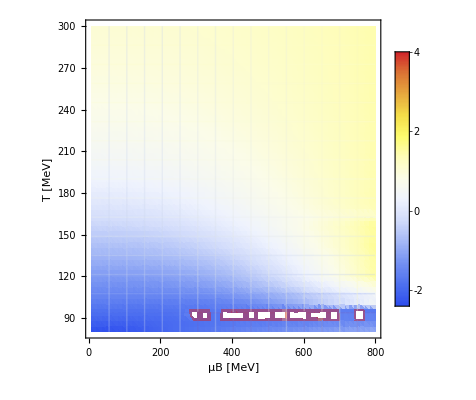

```mathematica
(*Flatten your data*)
flatData=Flatten[Pvals[[;;;;2,2;;;;2]],1];

(*Compute {x,y,avg z over selected indices}*)
results={#[[1]],#[[2]],#[[3]]}&/@flatData;

(*Apply logarithm safely*)
results[[All,3]]=Log[results[[All,3]]];  (*small shift to avoid log(0)*)

(*Plot heatmap*)
ListDensityPlot[results,ColorFunction->"TemperatureMap",InterpolationOrder->1,(*or 2 for smoother*)Frame->True,FrameLabel->{"μB [MeV]","T [MeV]"},PlotLegends->Automatic,Mesh->True]
```

```mathematica
P[[1,1,ind[[2]]]]
```

{A[1]→0.179392,A[2]→-0.384963,n[1]→-0.308908,n[2]→-0.330964}

```mathematica
f1*Product[(1+At[[i]]*t^2)^nt[[i]],{i,1,m}]/. P[[1,1,2]] /. t->1
```

0.139765

```mathematica
chivals = {};
P = Import["withpressureNsolvenewnewnew.mx"];
aux = {};
For[i=1,i <= Length[Ttable],i++,
m=2;
At=Table[A[i],{i,1,m}];
nt=Table[n[i],{i,1,m}];
f0=1;
f1=chi2list⟦i⟧/(2! Plist⟦i⟧)*2;
fnum = 0;
For[k = 1,k<=Length[P[[i,1]]],k++,
F2num=Evaluate[f1*Product[(1+At[[i]]*t^2)^nt[[i]],{i,1,m}]/. P[[i,1,k]]];
fnum += F2num/Length[P[[i,1]]];
];
aux = {};
For[j=1,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,Abs[Plist⟦i⟧*fnum /.t->μtable⟦i,j⟧]}];
	];
AppendTo[chivals,aux];
];
```

```mathematica
ListPointPlot3D[Flatten[chivals,1],AxesLabel->{"μ","T","P"},PlotRange->{{0,800},{80,300},{0,0.5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

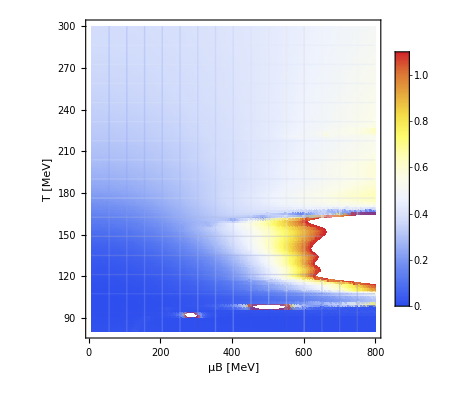

0.13138

```mathematica
(*Flatten your data*)
flatData=Flatten[chivals[[;;,2;;]],1];

(*Compute {x,y,avg z over selected indices}*)
results={#[[1]],#[[2]],#[[3]]}&/@flatData;

(*Apply logarithm safely*)
results[[All,3]]=results[[All,3]];  (*small shift to avoid log(0)*)

(*Plot heatmap*)
ListDensityPlot[results,ColorFunction->"TemperatureMap",InterpolationOrder->1,(*or 2 for smoother*)Frame->True,FrameLabel->{"μB [MeV]","T [MeV]"},PlotLegends->Automatic,Mesh->True]
```

```mathematica
ListPointPlot3D[Flatten[chivals,1],AxesLabel->{"μ","T","P"},PlotRange->{{0,600},{100,300},{0,5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

```mathematica
P={};
For[i=1,i≤Length[Ttable],i++,
coeffs = {1,0,chi2list⟦i⟧/(2! Plist⟦i⟧),0,chi4list⟦i⟧/(4! Plist⟦i⟧),0,chi6list⟦i⟧/(6! Plist⟦i⟧),0,chi8list⟦i⟧/(8! Plist⟦i⟧),0,chi10list⟦i⟧/(10! Plist⟦i⟧)};
x=Symbol["x"];k=Length[coeffs]-1;m=2;At=Table[A[i],{i,1,m}];nt=Table[n[i],{i,1,m}];
f0=1;
f1=chi2list⟦i⟧/(2! Plist⟦i⟧)*2;
F2=f1*Product[(1+At[[i]]*t^2)^nt[[i]],{i,1,m}];

F2series = Normal[Series[F2,{t,0,k}]];

Gpoly:=f0+Integrate[(x-t) F2series,{t,0,x}];

Gseries:=  Normal[Series[Gpoly,{x,0,k}]];
(*---Create equations by matching coefficients---*)

equations=Table[Coefficient[Gseries,x,j]==coeffs[[j+1]],{j,0,k}];
(*Maybe also AppendTo[equaitons,Total[nt]==2] or something*)

(*---Solve for parameters---*)
(*Solve over reals, maybe the exponents could be complex for DSI*)
solutions=NSolve[equations[[5;;;;2]],Join[At,nt],Reals,Method-> "Polynomial"];

aux = {{solutions}};

F2num=Function[t,Evaluate[f1*Product[(1+At[[i]]*t^2)^nt[[i]],{i,1,m}]/. solutions[[1]]]];
Gnum=Function[mu,f0+NIntegrate[(mu-t) F2num[t],{t,0,mu}]];

For[j=1,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,Gnum[μtable⟦i,j⟧]}];
];
AppendTo[P,aux];
Print[i];
Export["withpressureNsolvenewnewnewreals.mx",P]];
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand (6/41-t) (-0.00269411 (1+t^2 A[1])^n[1] (1+t^2 A[2])^n[2]/.{}⟦1⟧) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6/41}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1

2

3

4

5

6

7

8

9

10

11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.42946}. NIntegrate obtained 0.211634+0.000129791 ⅈ and 2.95517×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.43056}. NIntegrate obtained 0.241867+0.000315967 ⅈ and 7.96431×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.42946}. NIntegrate obtained 0.274981+0.000590175 ⅈ and 6.17401×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

12

13

14

15

16

Part::partw: Part 1 of {} does not exist.

17

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

```mathematica
P = Import["withpressureNsolvenewnewnewreals.mx"];
```

```mathematica
P[[2;;3,1]]
```

{{{{A[1]→0.16537,A[2]→2.32729,n[1]→0.447783,n[2]→0.998179},{A[1]→2.32729,A[2]→0.16537,n[1]→0.998179,n[2]→0.447783}}},{{{A[1]→0.513898,A[2]→0.135307,n[1]→0.869547,n[2]→1.06433},{A[1]→0.135307,A[2]→0.513898,n[1]→1.06433,n[2]→0.869547}}}}

```mathematica
P = Import["withpressureNsolvenewnewnewreals.mx"];
For[i=1,i<=Length[P],i++,
P[[i,2;;,3]] = P[[i,2;;,3]]*Plist[[i]]
]

results = {#[[1]],#[[2]],Re[#[[3]]]} &/@Flatten[P[[;;,2;;]],1];
```

```mathematica
ListPointPlot3D[results[[;;]],AxesLabel->{"μ","T","P"},PlotRange->{{0,600},{100,300},{0,5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

```mathematica
P[[17,1,1]]
```

{}

```mathematica
chi = {};
P = Import["withpressureNsolvenewnewnewreals.mx"];
For[i=1,i<=Length[P],i++,
P[[i,2;;,3]] = P[[i,2;;,3]]*Plist[[i]]
]

aux = {};
For[i=2,i <= Length[Ttable],i++,
m=2;At=Table[A[i],{i,1,m}];nt=Table[n[i],{i,1,m}];
If[P[[i,1,1]]==={},Print["empty"],
F2num=Function[t,Evaluate[f1*Product[(1+At[[i]]*t^2)^nt[[i]],{i,1,m}]/. P[[i,1,1,2]]]];
For[j=2,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,Plist⟦i⟧*F2num[μtable⟦i,j⟧]}];
];
];
AppendTo[chi,aux];
]
```

empty

empty

empty

Part::partw: Part 2 of {{A[1]→-0.144923,A[2]→0.171425,n[1]→-0.0231058,n[2]→0.435073}} does not exist.

ReplaceAll::reps: {{{{{}},{0,100,0.176},{600/41,100,0.176008},{1200/41,100,0.176032},{1800/41,100,0.176074},«34»,{22800/41,100,0.403622},{23400/41,100,0.431445},{24000/41,100,0.461956},{600,100,0.495345}},«39»,{«1»}}⟦«1»⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of {{A[1]→0.0285172,A[2]→0.159837,n[1]→0.492904,n[2]→0.35292}} does not exist.

Part::partw: Part 2 of {{A[1]→0.0544296,A[2]→0.156491,n[1]→0.412196,n[2]→0.286852}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
chi[[1]] //Length
```

41

```mathematica
ListPointPlot3D[Flatten[chi,1],AxesLabel->{"μ","T","chi"},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

```mathematica
P = Import["withpressuregoal.mx"];
results = {#[[1]],#[[2]],Re[#[[3]]]}&/@P;
```

```mathematica
ListPointPlot3D[results,AxesLabel->{"μ","T","P"},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

### Without pressure new:

```mathematica
Ttable = Table[i,{i,100,300,5}];
μtable = Table[i/j,{j,100,300,5},{i,0,600,600/Length[Ttable]}];
chi2func[T_] = Interpolation[chi2][T];
chi4func[T_] = Interpolation[chi4][T];
chi6func[T_] = Interpolation[chi6][T];
chi8func[T_] = Interpolation[chi8][T];
chi10func[T_] = Interpolation[chi10][T];

chi2list = chi2func[Ttable];
chi4list = chi4func[Ttable];
chi6list = chi6func[Ttable];
chi8list = chi8func[Ttable];
chi10list = chi10func[Ttable];
```

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
chi={};
For[i=1,i≤Length[Ttable],i++,coeffs={1,chi4list⟦i⟧/(2! chi2list⟦i⟧),chi6list⟦i⟧/(4! chi2list⟦i⟧),chi8list⟦i⟧/(6!chi2list⟦i⟧),chi10list⟦i⟧/(8! chi2list⟦i⟧)};

constraint ={{{1,1,1},1}};

factorapprox=chi2list⟦i⟧*FactorApproximantComplexConstrained[coeffs,constraint]/. x-> μ^2;

aux = {};
For[j=1,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,factorapprox/.μ->μtable⟦i,j⟧}];
];

AppendTo[chi,aux];
Print[i];
Export["withoutpressureNsolvenew.mx",chi]];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

```mathematica
chi = Import["withoutpressureNsolvenew.mx"];
results = {#[[1]],#[[2]],Re[#[[3]]]} &/@Flatten[chi[[;;,2;;]],1];
```

```mathematica
ListPointPlot3D[results[[;;]],AxesLabel->{"μ","T","chi"},PlotRange->{{0,600},{100,300},{0,0.5}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

### Without pressure:

```mathematica
Ttable = Table[i,{i,100,300,5}];
μtable = Table[i/j,{j,100,300,5},{i,0,600,600/Length[Ttable]}];
chi2func[T_] = Interpolation[chi2][T];
chi4func[T_] = Interpolation[chi4][T];
chi6func[T_] = Interpolation[chi6][T];
chi8func[T_] = Interpolation[chi8][T];
chi10func[T_] = Interpolation[chi10][T];

chi2list = chi2func[Ttable];
chi4list = chi4func[Ttable];
chi6list = chi6func[Ttable];
chi8list = chi8func[Ttable];
chi10list = chi10func[Ttable];
```

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
chi = {};
For[i=1,i<=Length[Ttable],i++,
(*---Input---*)(*Coefficients of the series:f(x)~1+a1 x+a2 x^2+...*)

coeffs={1,chi4list[[i]]/(2!chi2list[[i]]),chi6list[[i]]/(4!chi2list[[i]]),chi8list[[i]]/(6!chi2list[[i]]),chi10list[[i]]/(8!chi2list[[i]])};  (*example:1+2 x+3 x^2*)

x=Symbol["x"];
k=Length[coeffs]-1;
m=k/2; (*number of factors*)

(*---Define symbolic parameters for factor approximant---*)
At=Table[A[j],{j,1,m}];
nt=Table[n[j],{j,1,m}];

(*---Construct factor approximant---*)
factorApprox=Times@@Table[(1+At[[i]] x)^nt[[i]],{i,1,m}];

(*---Expand and collect series---*)
seriesApprox=Normal[Series[factorApprox,{x,0,k}]];

(*---Create equations by matching coefficients---*)
equations=Table[Coefficient[seriesApprox,x,j-1]==coeffs[[j]],{j,1,k+1}];

(*---Solve for parameters---*)
solutions=Solve[equations,Join[At,nt]];

(*---Factor approximant with solved parameters---*)
factorApproximant=chi2list[[i]]*factorApprox/. solutions[[1]] /. x-> μ^2;

For[j =1,j<=Length[μtable[[i]]],j++,
AppendTo[chi,{μtable[[i,j]]*Ttable[[i]],Ttable[[i]],factorApproximant/.μ -> μtable[[i,j]]}];
];

];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
ListPointPlot3D[Re[chi[[;;;;5]]],AxesLabel->{"μ","T","chi2"},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

### Without pressure with scaling limit data:

```mathematica
Ttable = Table[i,{i,100,300,5}];
μtable = Table[i/j,{j,100,300,5},{i,0,600,600/Length[Ttable]}];
chi2func[T_] = Interpolation[chi2][T];
chi4func[T_] = Interpolation[chi4][T];
chi6func[T_] = Interpolation[chi6][T];
chi8func[T_] = Interpolation[chi8][T];
chi10func[T_] = Interpolation[chi10][T];

chi2list = chi2func[Ttable];
chi4list = chi4func[Ttable];
chi6list = chi6func[Ttable];
chi8list = chi8func[Ttable];
chi10list = chi10func[Ttable];
```

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
chi = {};
For[i=1,i<=Length[Ttable],i++,

coeffs={1,chi4list[[i]]/(2!chi2list[[i]]),chi6list[[i]]/(4!chi2list[[i]]),chi8list[[i]]/(6!chi2list[[i]]),chi10list[[i]]/(8!chi2list[[i]])};  (*example:1+2 x+3 x^2*)

x=Symbol["x"];
k=Length[coeffs]-1;
m=k/2+1; (*number of factors*)

(*---Define symbolic parameters for factor approximant---*)
At=Table[A[j],{j,1,m}];
nt=Table[n[j],{j,1,m}];

(*---Construct factor approximant---*)
factorApprox=Times@@Table[(1+At[[i]] x)^nt[[i]],{i,1,m}];

(*---Expand and collect series---*)
seriesApprox=Normal[Series[factorApprox,{x,0,k}]];

(*---Create equations by matching coefficients---*)
equations=Table[Coefficient[seriesApprox,x,j-1]==coeffs[[j]],{j,1,k+1}];
AppendTo[equations ,Total[nt]==1];

solutions=NSolve[equations,Join[At,nt],Method->"Polynomial"];

(*---Factor approximant with solved parameters---*)
factorApproximant=chi2list[[i]]*factorApprox/. solutions /. x-> μ^2;
If[Length[solutions]>=1,
aux ={{factorApproximant}};
For[j=1,j≤Length[μtable⟦i⟧],j++,
AppendTo[aux,{μtable⟦i,j⟧ Ttable⟦i⟧,Ttable⟦i⟧,factorApproximant/.μ->μtable⟦i,j⟧}];];

AppendTo[chi,aux];
];
Export["withoutpressureNsolver.mx",P];
Print[i];

];
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

1

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

2

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 A[1])/30458+(20993 A[2])/30458-(27178 A[3])/45687-(71297 n[1])/91374-(173881 n[2])/182748+(11342 n[3])/15229 == 1.

General::stop: Further output of NSolve::infsolns will be suppressed during this calculation.

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

```mathematica
chi = Import["withoutpressureNsolvereals.mx"];
results = {#[[1]],#[[2]],Re[#[[3,2]]]} &/@Flatten[chi[[;;,2;;]],1];
```

```mathematica
ListPointPlot3D[results[[;;]],AxesLabel->{"μ","T","chi"},PlotRange->{{0,600},{100,300},{0,2}},PlotStyle->{Red,PointSize[Small]},Boxed->True]
```

-Graphics3D-

### Lattice data and func:

```mathematica
ClearAll[FactorApproximantComplexConstrained]
FactorApproximantComplexConstrained[coeffs_List,constraints_:{}]:=Module[{k,m,gSeries,logSeries,bList,pList,hankel,rhs,q,poly,Aroots,mRoots,vandermonde,extendedMatrix,extendedRHS,alphas,factorApprox,C,R,adjustedConstraints},(*---Step 1:series order and number of factors---*)k=Length[coeffs]-1;
m=Floor[k/2];
(*---Step 2:logarithmic series and power sums---*)gSeries=Sum[coeffs[[j+1]] x^j,{j,0,k}];
logSeries=Normal[Series[Log[gSeries],{x,0,k}]];
bList=Table[Coefficient[logSeries,x,i],{i,1,k}];
pList=Table[(-1)^(i+1) i bList[[i]],{i,1,k}];
(*---Step 3:Hankel system for Prony polynomial---*)hankel=Table[pList[[i+j-1]],{i,1,m},{j,1,m}];
rhs=-Table[pList[[m+i]],{i,1,m}];
q=LinearSolve[hankel,rhs];
(*---Step 4:Prony polynomial and numeric roots (complex allowed)---*)poly=1+Sum[q[[j]] z^j,{j,1,m}];
Aroots=1/(z/. NSolve[poly==0,z]);
mRoots=Length[Aroots];
(*---Step 5:Vandermonde system for alpha_j---*)vandermonde=Table[Aroots[[j]]^i,{i,1,mRoots},{j,1,mRoots}];
(*---Step 6:Adjust constraints length---*)adjustedConstraints=Table[{PadRight[constraints[[i,1]],mRoots],constraints[[i,2]]},{i,Length[constraints]}];
(*---Step 7:Build extended system if constraints exist---*)If[adjustedConstraints=!={},extendedMatrix=vandermonde;
extendedRHS=pList[[1;;mRoots]];
Do[{C,R}=adjustedConstraints[[i]];
extendedMatrix=Join[extendedMatrix,{C}];
extendedRHS=Join[extendedRHS,{R}],{i,Length[adjustedConstraints]}];
(*Use LeastSquares if overdetermined*)alphas=LeastSquares[extendedMatrix,extendedRHS],alphas=LinearSolve[vandermonde,pList[[1;;mRoots]]]];
(*---Step 8:Construct factor approximant---*)factorApprox=Times@@Table[(1+Aroots[[j]] x)^alphas[[j]],{j,1,mRoots}];
factorApprox]
```

```mathematica
ClearAll[FactorApproximantConstrainedComplex]
FactorApproximantConstrainedComplex[coeffs_List,constraints_:{}]:=Module[{k,m,gSeries,logSeries,bList,pList,hankel,rhs,q,poly,roots,Aroots,vandermonde,extendedMatrix,extendedRHS,alphas,factorApprox,C,R},(*---Step 1:series order and safe number of factors---*)k=Length[coeffs]-1;
m=Floor[k/2];
(*---Step 2:logarithmic series and power sums---*)gSeries=Sum[coeffs[[j+1]] x^j,{j,0,k}];
logSeries=Normal[Series[Log[gSeries],{x,0,k}]];
bList=Table[Coefficient[logSeries,x,i],{i,1,k}];
pList=Table[(-1)^(i+1) i bList[[i]],{i,1,k}];
(*---Step 3:Hankel system for q_j---*)hankel=Table[pList[[i+j-1]],{i,1,m},{j,1,m}];
rhs=-Table[pList[[m+i]],{i,1,m}];
q=LinearSolve[hankel,rhs];
(*---Step 4:Prony polynomial and numeric roots (complex allowed)---*)poly=1+Sum[q[[j]] z^j,{j,1,m}];
Aroots=1/(z/. NSolve[poly==0,z]);
mRoots=Length[Aroots];
(*---Step 5:Vandermonde system for alpha_j---*)vandermonde=Table[Aroots[[j]]^i,{i,1,mRoots},{j,1,mRoots}];
(*---Step 6:Incorporate linear constraints (optional)---*)If[constraints=!={},extendedMatrix=vandermonde;
extendedRHS=pList[[1;;mRoots]];
Do[{C,R}=constraints[[i]];
extendedMatrix=Join[extendedMatrix,{C}];
extendedRHS=Join[extendedRHS,{R}],{i,Length[constraints]}];
alphas=LinearSolve[extendedMatrix,extendedRHS],alphas=LinearSolve[vandermonde,pList[[1;;mRoots]]]];
(*---Step 7:Construct factor approximant---*)factorApprox=Times@@Table[(1+Aroots[[j]] x)^alphas[[j]],{j,1,mRoots}];
factorApprox]
```

```mathematica
ClearAll[FactorApproximantConstrained]
FactorApproximantConstrained[coeffs_List,constraints_:{}]:=Module[{k,m,gSeries,logSeries,bList,pList,hankel,rhs,q,poly,roots,realRoots,Aroots,mReal,vandermonde,extendedMatrix,extendedRHS,alphas,factorApprox,C,R},(*---Step 1:series order and safe number of factors---*)k=Length[coeffs]-1;
m=Floor[k/2];
(*---Step 2:logarithmic series and power sums---*)gSeries=Sum[coeffs[[j+1]] x^j,{j,0,k}];
logSeries=Normal[Series[Log[gSeries],{x,0,k}]];
bList=Table[Coefficient[logSeries,x,i],{i,1,k}];
pList=Table[(-1)^(i+1) i bList[[i]],{i,1,k}];
(*---Step 3:Hankel system for q_j---*)hankel=Table[pList[[i+j-1]],{i,1,m},{j,1,m}];
rhs=-Table[pList[[m+i]],{i,1,m}];
q=LinearSolve[hankel,rhs];
(*---Step 4:Prony polynomial and numeric roots---*)poly=1+Sum[q[[j]] z^j,{j,1,m}];
roots=z/. NSolve[poly==0,z];
realRoots=Select[N[roots],Im[#]==0&];
If[Length[realRoots]==0,Return[$Failed]];
Aroots=1/realRoots;
mReal=Length[Aroots];
(*---Step 5:Vandermonde system for alpha_j---*)vandermonde=Table[Aroots[[j]]^i,{i,1,mReal},{j,1,mReal}];
(*---Step 6:Incorporate linear constraints (optional)---*)If[constraints=!={},(*constraints should be a list of {C,R},where C is coeff list,R is target*)extendedMatrix=vandermonde;
extendedRHS=pList[[1;;mReal]];
Do[{C,R}=constraints[[i]];
extendedMatrix=Join[extendedMatrix,{C}];
extendedRHS=Join[extendedRHS,{R}],{i,Length[constraints]}];
alphas=LinearSolve[extendedMatrix,extendedRHS],(*No constraints*)alphas=LinearSolve[vandermonde,pList[[1;;mReal]]]];
(*---Step 7:Construct numeric factor approximant---*)factorApprox=N[Times@@Table[(1+Aroots[[j]] x)^alphas[[j]],{j,1,mReal}]];
factorApprox]
```

```mathematica
ClearAll[FactorApproximantReal]
FactorApproximantReal[coeffs_List]:=Module[{k,m,gSeries,logSeries,bList,pList,hankel,rhs,q,poly,roots,realRoots,Aroots,vandermonde,alphas,factorApprox},(*---Step 1:series order and safe number of factors---*)k=Length[coeffs]-1;
m=Floor[k/2];
(*---Step 2:logarithmic series and power sums---*)gSeries=Sum[coeffs[[j+1]] x^j,{j,0,k}];
logSeries=Normal[Series[Log[gSeries],{x,0,k}]];
bList=Table[Coefficient[logSeries,x,i],{i,1,k}];
pList=Table[(-1)^(i+1) i bList[[i]],{i,1,k}];
(*---Step 3:Hankel system for q_j---*)hankel=Table[pList[[i+j-1]],{i,1,m},{j,1,m}];
rhs=-Table[pList[[m+i]],{i,1,m}];
q=LinearSolve[hankel,rhs];
(*---Step 4:Prony polynomial and numeric roots---*)poly=1+Sum[q[[j]] z^j,{j,1,m}];
roots=z/. NSolve[poly==0,z];
(*---Keep only real roots---*)realRoots=Select[N[roots],Im[#]==0&];
If[Length[realRoots]==0,Return[$Failed,Module]];
Aroots=1/realRoots;
(*---Step 5:Vandermonde system for alpha_j---*)mReal=Length[Aroots];
vandermonde=Table[Aroots[[j]]^i,{i,1,mReal},{j,1,mReal}];
alphas=LinearSolve[vandermonde,pList[[1;;mReal]]];
(*---Step 6:construct numeric factor approximant---*)factorApprox=N[Times@@Table[(1+Aroots[[j]] x)^alphas[[j]],{j,1,mReal}]];
factorApprox]
```

```mathematica
ClearAll[FactorApproximant]
FactorApproximant[coeffs_List]:=Module[{k,m,gSeries,logSeries,bList,pList,hankel,rhs,q,poly,roots,Aroots,vandermonde,alphas,factorApprox},(*---Step 1:series order and safe number of factors---*)k=Length[coeffs]-1;(*series order*)m=Floor[k/2];(*maximum safe factors*)(*---Step 2:logarithmic series and power sums---*)gSeries=Sum[coeffs[[j+1]] x^j,{j,0,k}];
logSeries=Normal[Series[Log[gSeries],{x,0,k}]];
bList=Table[Coefficient[logSeries,x,i],{i,1,k}];
pList=Table[(-1)^(i+1) i bList[[i]],{i,1,k}];
(*---Step 3:construct Hankel system for q_j---*)hankel=Table[pList[[i+j-1]],{i,1,m},{j,1,m}];
rhs=-Table[pList[[m+i]],{i,1,m}];
q=LinearSolve[hankel,rhs];
(*---Step 4:Prony polynomial and numeric roots---*)poly=1+Sum[q[[j]] z^j,{j,1,m}];
roots=z/. NSolve[poly==0,z];
Aroots=1/N[roots];
(*---Step 5:Vandermonde system for alpha_j---*)vandermonde=Table[Aroots[[j]]^i,{i,1,m},{j,1,m}];
alphas=LinearSolve[vandermonde,pList[[1;;m]]];
(*---Step 6:construct numeric factor approximant---*)factorApprox=N[Times@@Table[(1+Aroots[[j]] x)^alphas[[j]],{j,1,m}]];
factorApprox]
```

```mathematica
(*From 1309.5258*)
Pdata = Table[{Import["WB-EoS.dat.txt","Table"][[2;;,1]][[i]],Import["WB-EoS.dat.txt","Table"][[2;;,4]][[i]]},{i,Length[Import["WB-EoS.dat.txt","Table"][[2;;,1]]]}];

AppendTo[Pdata,{0,0}]
(*From 2507.13254*)
chi2 = Import["chi2.csv"][[2;;,{1,2}]];
AppendTo[chi2,{50,0}]
chi4= Import["chi4.csv"][[2;;,{1,2}]];
AppendTo[chi4,{50,0}]
chi6 =  Import["chi6.csv"][[2;;,{1,2}]];
AppendTo[chi6,{50,0}]
chi8 =  Import["chi8.csv"][[2;;,{1,2}]];
AppendTo[chi8,{50,0}]
chi10 =  Import["chi10.csv"][[2;;,{1,2}]];
AppendTo[chi10,{50,0}]
```

{{110,0.242},{115,0.274},{120,0.308},{125,0.348},{130,0.393},{135,0.444},{140,0.501},{145,0.565},{150,0.633},{155,0.712},{160,0.798},{165,0.886},{170,0.981},{175,1.08},{180,1.18},{185,1.28},{190,1.39},{195,1.49},{200,1.58},{205,1.68},{210,1.77},{215,1.86},{220,1.95},{225,2.03},{230,2.12},{235,2.2},{240,2.27},{245,2.35},{250,2.42},{260,2.55},{270,2.68},{280,2.78},{290,2.89},{300,2.98},{310,3.07},{320,3.15},{330,3.23},{340,3.29},{350,3.36},{360,3.41},{370,3.47},{380,3.52},{390,3.56},{400,3.6},{410,3.64},{420,3.68},{430,3.71},{440,3.74},{445,3.76},{450,3.77},{455,3.79},{460,3.8},{465,3.81},{470,3.82},{475,3.84},{480,3.85},{485,3.86},{490,3.87},{495,3.88},{500,3.89},{505,3.9},{510,3.91},{0,0}}

{{99.8985,-0.000410809},{105.316,0.00109209},{110.164,0.00560333},{115.027,0.00849175},{120.088,0.0132352},{124.815,0.0199255},{130.397,0.0271542},{134.559,0.0346814},{139.784,0.0462479},{145.477,0.0616647},{149.551,0.0780511},{155.197,0.0993111},{160.016,0.121525},{164.939,0.146238},{169.816,0.170292},{174.807,0.194501},{179.688,0.215955},{184.93,0.233954},{189.677,0.250815},{194.673,0.264816},{199.753,0.277508},{204.595,0.288952},{209.559,0.297328},{219.749,0.315514},{229.853,0.326588},{240.173,0.338004},{249.686,0.34697},{259.861,0.353648},{280.198,0.365275},{299.89,0.373119},{50,0}}

{{99.8661,0.00248084},{104.98,0.00405699},{109.916,0.00639948},{114.927,0.00946704},{120.009,0.0139927},{124.685,0.0188095},{129.953,0.0260861},{135.025,0.0342994},{139.68,0.04598},{145.058,0.0590875},{150.011,0.0721791},{154.868,0.0843022},{159.848,0.0955961},{164.653,0.100045},{169.991,0.102348},{175.384,0.0972859},{180.195,0.0910596},{184.735,0.0836308},{189.708,0.0759985},{194.849,0.0691325},{199.815,0.0639869},{205.091,0.0592997},{209.646,0.0554144},{219.622,0.0493887},{230.136,0.0460162},{239.958,0.0435701},{249.851,0.0412131},{259.473,0.0398695},{279.771,0.0381724},{299.631,0.037012},{50,0}}

{{100.216,0.00226187},{105.337,0.00350831},{110.176,0.00666423},{114.906,0.00934847},{119.98,0.0143797},{124.705,0.0178139},{129.901,0.0238341},{134.93,0.0329212},{140.006,0.0403336},{144.733,0.0461717},{150.54,0.0405208},{154.691,0.0296535},{159.453,0.00119541},{164.54,-0.0320561},{170.102,-0.0704868},{174.983,-0.0851151},{179.713,-0.094826},{185.673,-0.0888751},{189.986,-0.0786502},{195.194,-0.0660689},{200.254,-0.0513764},{204.175,-0.0430723},{209.396,-0.0360985},{219.927,-0.0236599},{229.596,-0.0176843},{239.671,-0.0126985},{249.499,-0.00968534},{259.155,-0.00745416},{279.6,-0.00490025},{299.807,-0.00336315},{50,0}}

{{100.093,0.00106011},{104.872,-0.00260365},{109.983,0.00390873},{114.585,0.00530486},{119.764,0.0159796},{124.825,0.0164089},{129.615,0.0152512},{134.984,0.0032627},{139.573,0.00126822},{144.797,-0.0256181},{149.468,-0.0822221},{154.793,-0.169827},{159.59,-0.243796},{165.955,-0.201964},{170.6,-0.0431998},{173.844,0.0836529},{178.944,0.259717},{184.716,0.302759},{189.928,0.267244},{194.532,0.271849},{199.889,0.20594},{204.705,0.174623},{208.78,0.145815},{220.111,0.0800108},{229.11,0.0518151},{239.233,0.0318617},{249.585,0.0234979},{259.227,0.0185334},{279.15,0.0105078},{298.944,0.00628475},{50,0}}

{{100.706,-0.0128046},{104.884,-0.119683},{109.96,-0.0868061},{114.784,-0.111839},{119.915,-0.0445854},{125.052,-0.0873252},{129.584,-0.0204758},{135.232,-0.0967844},{139.813,-0.144138},{145.227,-0.675242},{149.762,-0.929661},{155.057,-0.259841},{160.07,0.712098},{165.028,1.53627},{169.861,2.009},{174.873,1.11856},{180.139,-0.0872675},{184.681,-0.874001},{189.442,-1.29073},{195.011,-1.31645},{199.919,-1.11175},{204.962,-0.932949},{209.574,-0.709387},{219.804,-0.395789},{229.883,-0.306215},{239.439,-0.184571},{249.353,-0.149214},{259.773,-0.0715789},{279.651,-0.0375487},{299.79,-0.0351262},{50,0}}

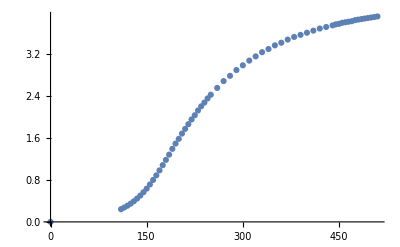

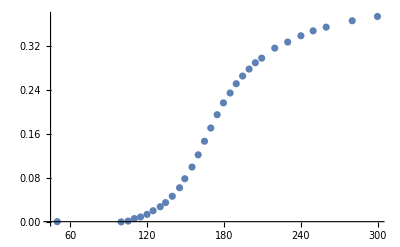

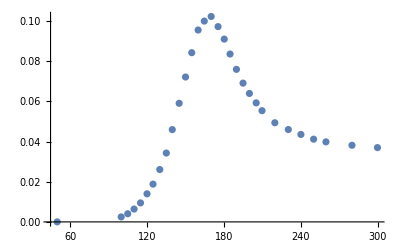

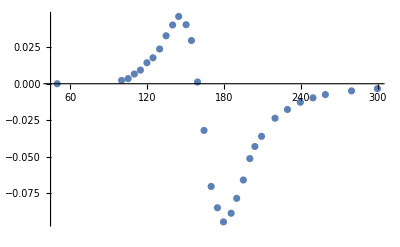

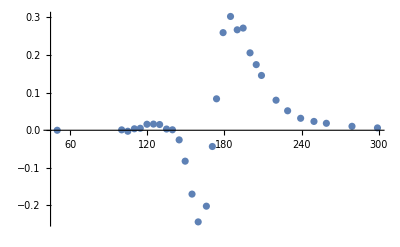

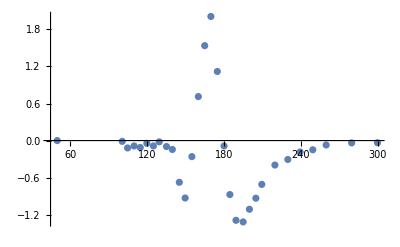

```mathematica
ListPlot[Pdata]
ListPlot[chi2]
ListPlot[chi4]
ListPlot[chi6]
ListPlot[chi8]
ListPlot[chi10]
```